```mathematica
dataUpTo7=Import[FileNameJoin[{NotebookDirectory[],ToString[#]}]][[All,3;;4]]&/@Range[2,7]
```

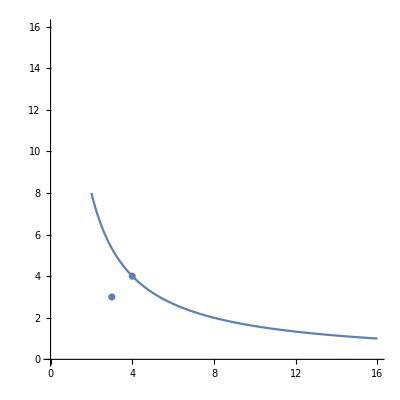
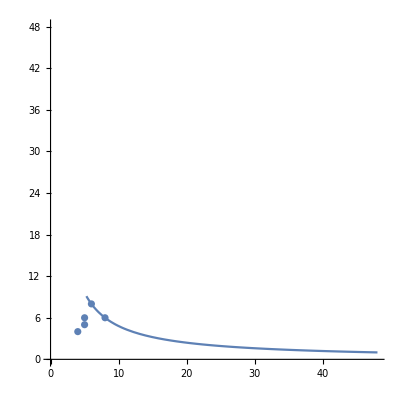
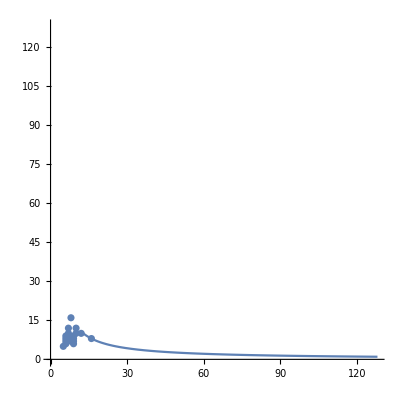
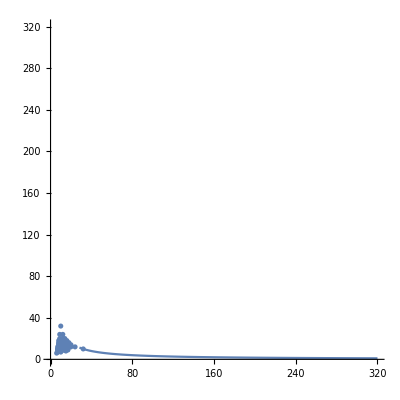
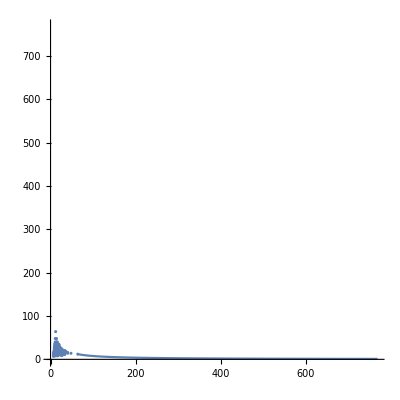
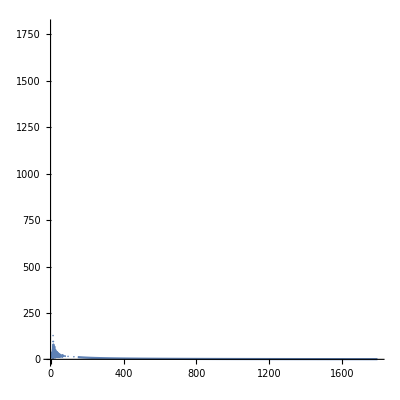

```mathematica
MapIndexed[Show[ListPlot[#1,PlotRange->{{0,(#2[[1]]+1)2^(#2[[1]]+2)},{0,(#2[[1]]+1)2^(#2[[1]]+2)}},PlotStyle->Thick,AxesOrigin->{0,0},AspectRatio->1],Plot[2*(2^(#2[[1]]+1)×(#2[[1]]+1))/x,{x,(#2[[1]]+1),(#2[[1]]+1)2^(#2[[1]]+2)}]]&,dataUpTo7]
```